## The horizon problem

Particle horizon: 
用红移  做变量：

```mathematica
Subscript[Ω, Λ]=0.69;
Subscript[Ω, m]=0.31;
Subscript[Ω, γ]=5*10^-5;
zCMB=1100;
H[z_]:= (√(Subscript[Ω, γ](1+z)^4+Subscript[Ω, m](1+z)^3+Subscript[Ω, Λ]))/QuantityMagnitude[UnitConvert[1/Quantity[, "HubbleParameter"],"Gyr"]]
{I1,I2}={NIntegrate[1/H[z],{z,0,Infinity}],NIntegrate[1/H[z],{z,zCMB,Infinity}]};
dHCMB=UnitConvert[Quantity[, "SpeedOfLight"]Quantity[, "Gigayears"] 1/(1+zCMB)I2,"Mpc"];
{dH0,dHCMB0}={UnitConvert[Quantity[, "SpeedOfLight"]Quantity[, "Gigayears"]I1,"Mpc"],(1+zCMB)dHCMB}
dHCMB0/dH0
```

{14250.1 Mpc,318.387 Mpc}

0.0223428

CMB 形成时的视界红移到当前时刻也远小于当前宇宙的视界尺度
意味着，我们观测到的CMB 是由大量不连通区域组成的
但是观测的CMB 具有高度均匀性（不均匀度），这是以上推论无法解释的！
-Graphics-

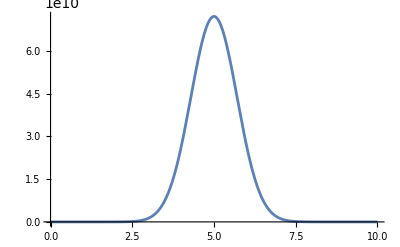

```mathematica
Plot[Exp[10t-1 t^2],{t,0,10}]
```

## Inflation

### 定性分析 inflation 阶段标量场演化

绘制标量场的相图，由运动方程（设） 
-Graphics-
取二次函数势，用 改写得到：
-Graphics-
取-Graphics-, 以及

NDSolve::ndinnt: 初始条件 n 不是一个数，也不是由数组成的矩形数组.

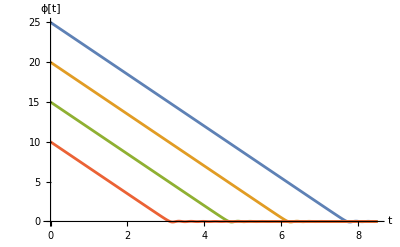

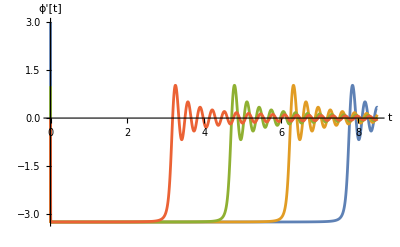

```mathematica
T=8.5;
eq1=y'[t]+√(12Pi(y[t]^2+400 x[t]^2))y[t]+400x[t]==0;
(*eq1=y[t] D[y[t],x[t]]==-√(12Pi(y[t]^2+400 x[t]^2))y[t]-400x[t];*)
eq2=y[t]==x'[t];
s=NDSolve[{eq1,eq2,x[0]==m,y[0]==n},{x[t],y[t]},{t,0,T}]/.{{m->25,n->3},{m->20,n->-2},{m->15,n->1},{m->10,n->0}};
Plot[Evaluate[x[t]/.s],{t,0,T},AxesLabel->{"t","ϕ[t]"}]
Plot[Evaluate[y[t]/.s],{t,0,T},AxesLabel->{"t","ϕ'[t]"}]
```

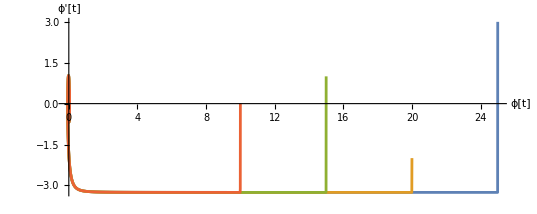

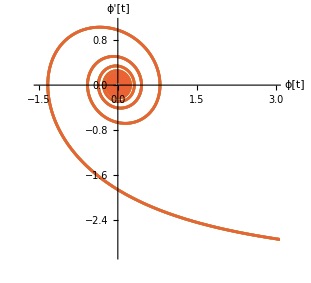

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/. s],{t,0,T},AxesLabel->{"ϕ[t]","ϕ'[t]"}]
ParametricPlot[Evaluate[{20*x[t],y[t]}/. s],{t,0,T},PlotRange->{{-1.5,3},{-3,1.1}},AxesLabel->{"ϕ[t]","ϕ'[t]"}]
```

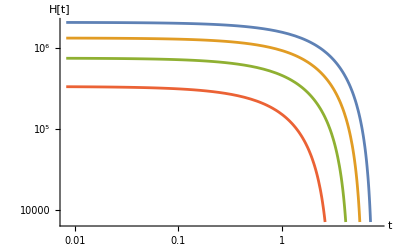

```mathematica
LogLogPlot[Evaluate[8/3 Pi(y[t]^2+400 x[t]^2)/. s],{t,0,T},AxesLabel->{"t","H[t]"}]
```

### Inflation 的严格数值求解

考虑一个平坦的宇宙，取自然单位制 
取二次函数势能 , 两个可调整的参数
对inflation 过程进行严格数值求解

```mathematica
mp=2.4*10^18;(*GeV*)
m=3*10^11;
T=1.2*10^-10;
V[ϕ_]:=1/2(m)^2 ϕ^2;
H[t]=√(1/(3 mp^2)(1/2 ϕ'[t]^2+V[ϕ[t]]));
eq1=ϕ''[t]+3H[t]*ϕ'[t]+D[V[ϕ[t]],ϕ[t]]==0;
solt=NDSolve[{eq1,ϕ[0]==20mp,ϕ'[0]==0},ϕ[t],{t,0,T}];
Plot[Evaluate[ϕ[t]/.solt],{t,0,T},AxesLabel->{"t / GeV^-1","ϕ [ t ] / GeV"}]
efolds=Table[{n,NIntegrate[Evaluate[√(1/(3 mp^2)(1/2 D[ϕ[t]/.solt,t]^2+V[ϕ[t]/.solt]))][[1]],{t,0,n}]},{n,0,T,5*10^-12}];
```

-Graphics-

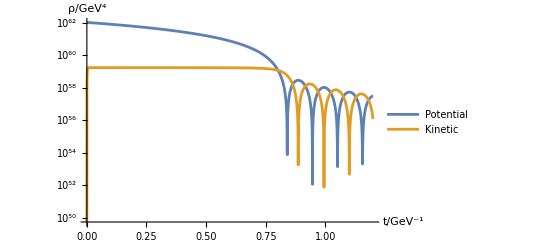

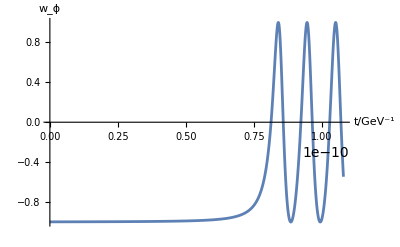

5.29202×10^-35

```mathematica
Po=1/2 m^2(ϕ[t]/. solt)^2;
Ki=1/2(D[ϕ[t]/. solt,t])^2;
LogPlot[Evaluate[{Po,Ki}],{t,0,T},AxesLabel->{"t/GeV^-1","ρ/GeV^4"},PlotLegends->Placed[{"Potential","Kinetic"}, {Top,Right}]]
Plot[Evaluate[{(Ki-2Po)/(Ki+2Po)}],{t,0,0.9T},AxesLabel->{"t/GeV^-1","w_ϕ"},PlotRange->All]
tend=8.04*10^-11 ;
UnitConvert[(tend Quantity[, "ReducedPlanckConstant"])/Quantity[, "Gigaelectronvolts"],"Seconds"];(*大致退出inflation 的时间，转换为国际单位制下*)
QuantityMagnitude[%]//N
```

Inflation 大部分时间，势能远大于动能，。
Inflation 结束后，标量场开始振荡，周期平均下，（inflaton condensation）
标量场近似的呈现非相对论性粒子的演化性质()。

101.208

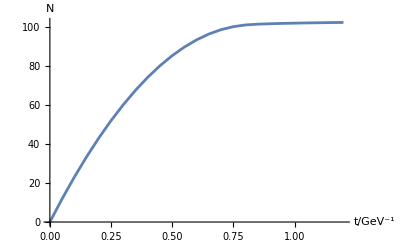

```mathematica
NIntegrate[Evaluate[√(1/(3 mp^2)(1/2 D[ϕ[t]/.solt,t]^2+V[ϕ[t]/.solt]))][[1]],{t,0,tend}]
ListLinePlot[efolds,AxesLabel->{"t/GeV^-1","N"}]
```

```mathematica
Plot[Evaluate[√((8Pi)/3(1/2 D[ϕ[t]/.solt,t]^2+V[ϕ[t]/.solt]))],{t,0,T},AxesLabel->{"t","H(t)"}]
Plot[Exp[((20mp)^2-(ϕ[t]/.solt)^2)/(4 mp^2)],{t,0,T},AxesLabel->{"t","(a (t))/(a (t = 0))"}]
Log[2.7*10^43](*e-flods*)
```

-Graphics-

-Graphics-

100.004

```mathematica
Plot[Evaluate[(-(ϕ[t]/.solt)*D[ϕ[t]/.solt,t])/(2 mp^2)Exp[((20mp)^2-(ϕ[t]/.solt)^2)/(4 mp^2)]],{t,0,T},AxesLabel->{"t","a'(t)"},PlotRange->All]
```

-Graphics-